```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
(*define everything as functions of r1,r2 or t*)
r[r1_,r2_]:=Abs[r1-r2];
(*m is a mass matrix, not a vector*)
m={{m1,0},{ 0,m2}};
M11 [r1_,r2_]:= 1/(6*π*η*a1);
(*(r1-r2)*(r1-r2) is suposed to be a dyadic product*)
(*I think you also had a typo in ((x1[t]-x2[t])*(x2[t]-x1[t]))*)
M12[r1_,r2_]:= 1/(8*π*η*r[r1,r2])*(1+TensorProduct[(r1-r2),(r1-r2)]/r[r1,r2]^2);
(*M12[r1_,r2_]:= 1/(4*π*η*r[r1,r2]);*)
M22 [r1_,r2_]:= 1/(6*π*η*a2);
M [r1_,r2_]:= {{M11[r1,r2], M12[r1,r2]},{M12[r1,r2], M22[r1,r2]}};
F12[r1_,r2_,t_]:= Fa*Cos[2*π * f *t]*((r1-r2)/r[r1,r2]);
(*Fa, aka the force amplitude, was renamed (used to be called F) since it was coinciding with the general force function, also called F:*)
F [r1_,r2_,t_]:= {F12[r1,r2,t], -F12[r1,r2,t]};
(**(x1[t]-x2[t])*)
G1[r1_,r2_]:=-k *(r [r1,r2]-L)*(r1-r2)/r[r1,r2]; 
G2[r1_,r2_]:=-G1[r1,r2];
G[r1_,r2_]:={G1[r1,r2], G2[r1,r2]};
```

```mathematica
(*input paramters*)
a1 = 5;
a2 = 8;
η = 1/6;
(*f =0.2*10^-3;
Fa = 0.05;*)
k = 1/200;
L = 28;
ρs = 8;
m1 = 4/3*π*a1^3*ρs;
m2 = 4/3*π*a2^3*ρs;
(*τ is the period length*)
τ=1/f;
```

```mathematica
sol=NDSolve[{{r1'[t], r2'[t]}==M[r1[t],r2[t]].(F[r1[t],r2[t],t]+G[r1[t],r2[t]]-m.{r1''[t],r2''[t]}),{ r1[0],r2[0]}=={-L,0}, { r1'[0],r2'[0]}=={0,0}}, {r1, r2}, {t, 0,100τ}]
```

NDSolve::ndnl: Endpoint 100./f in {t,0.,100./f} is not a real number.

NDSolve[{{r1'[t],r2'[t]}=={(-((-28+Abs[r1[t]-r2[t]]) (r1[t]-r2[t]))/(200 Abs[r1[t]-r2[t]])+(Fa Cos[2 f π t] (r1[t]-r2[t]))/Abs[r1[t]-r2[t]]-4000/3 π r1''[t])/(5 π)+(3 (1+((r1[t]-r2[t])⊗(r1[t]-r2[t]))/Abs[r1[t]-r2[t]]^2) (((-28+Abs[r1[t]-r2[t]]) (r1[t]-r2[t]))/(200 Abs[r1[t]-r2[t]])-(Fa Cos[2 f π t] (r1[t]-r2[t]))/Abs[r1[t]-r2[t]]-16384/3 π r2''[t]))/(4 π Abs[r1[t]-r2[t]]),(3 (1+((r1[t]-r2[t])⊗(r1[t]-r2[t]))/Abs[r1[t]-r2[t]]^2) (-((-28+Abs[r1[t]-r2[t]]) (r1[t]-r2[t]))/(200 Abs[r1[t]-r2[t]])+(Fa Cos[2 f π t] (r1[t]-r2[t]))/Abs[r1[t]-r2[t]]-4000/3 π r1''[t]))/(4 π Abs[r1[t]-r2[t]])+(((-28+Abs[r1[t]-r2[t]]) (r1[t]-r2[t]))/(200 Abs[r1[t]-r2[t]])-(Fa Cos[2 f π t] (r1[t]-r2[t]))/Abs[r1[t]-r2[t]]-16384/3 π r2''[t])/(8 π)},{r1[0],r2[0]}=={-28,0},{r1'[0],r2'[0]}=={0,0}},{r1,r2},{t,0,100/f}]

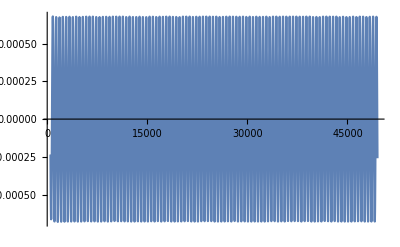

```mathematica
Plot[Evaluate[{(r1'[t]+r2'[t])/2}/.sol],{t,1τ, 99τ},PlotRange->All]
```

```mathematica
NIntegrate[Evaluate[1/τ*{(r1'[t]+r2'[t])/2}/.sol],{t,98τ,99τ}]
```

{{-2.49941×10^-6}}

```mathematica
(*
v_{ca}=1/T\int^{t_0}_{t_0-T} (\partial/ \partial t r1(t)+ \partial/ \partial t r2(t))/2 dt


V = 1/τ∫_(t0 - τ)^t0 (r1'[t]+r2'[t])/2 ⅆt

*)
```

```mathematica
num5b=Log[10,(*0.001*)800.];
num5e=Log[10,24000.];
TListNum=Table[10.^i,{i,num5b,num5e,(num5e-num5b)/15.}]//Reverse;
FList={0.05,0.07,(*0.1,*)0.12,0.15};
velListnum=ConstantArray[Null,{Length[FList],Length[TListNum]}]
```

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
Do[Fa=FList[[i]]; f=1/TListNum[[j]];
sol=NDSolve[{{r1'[t], r2'[t]}==M[r1[t],r2[t]].(F[r1[t],r2[t],t]+G[r1[t],r2[t]]-m.{r1''[t],r2''[t]}),{ r1[0],r2[0]}=={-L,0}, { r1'[0],r2'[0]}=={0,0}}, {r1, r2}, {t, 0,100/f}];
velListnum[[i,j]]={f*10^3,10^6*NIntegrate[Evaluate[f*{(r1'[t]+r2'[t])/2}/.sol],{t,98/f,99/f}][[1,1]]}; ,{i,1,Length[FList]},{j,1,Length[TListNum]}]
```

```mathematica
velListnum
```

{{{0.0416667,-1.66323},{0.0522713,-2.17167},{0.065575,-2.6687},{0.0822646,-3.06169},{0.103202,-3.26195},{0.129468,-3.21675},{0.162419,-2.92852},{0.203757,-2.45582},{0.255615,-1.89416},{0.320672,-1.34373},{0.402287,-0.877988},{0.504674,-0.529509},{0.63312,-0.295768},{0.794256,-0.153732},{0.996404,-0.0749182},{1.25,-0.0343035}},{{0.0416667,-3.15222},{0.0522713,-4.14431},{0.065575,-5.12853},{0.0822646,-5.92081},{0.103202,-6.33942},{0.129468,-6.27309},{0.162419,-5.72354},{0.203757,-4.80577},{0.255615,-3.70926},{0.320672,-2.63243},{0.402287,-1.72042},{0.504674,-1.03775},{0.63312,-0.579606},{0.794256,-0.301448},{0.996404,-0.147621},{1.25,-0.0678471}},{{0.0416667,-7.29124},{0.0522713,-10.1613},{0.065575,-13.3508},{0.0822646,-16.1444},{0.103202,-17.8371},{0.129468,-17.9954},{0.162419,-16.6019},{0.203757,-14.0243},{0.255615,-10.86},{0.320672,-7.72115},{0.402287,-5.05105},{0.504674,-3.04854},{0.63312,-1.70323},{0.794256,-0.885575},{0.996404,-0.431965},{1.25,-0.199917}},{{0.0416667,-14.4829},{0.0522713,-13.8803},{0.065575,-18.1057},{0.0822646,-23.053},{0.103202,-26.5127},{0.129468,-27.392},{0.162419,-25.5955},{0.203757,-21.7636},{0.255615,-16.9092},{0.320672,-12.0427},{0.402287,-7.88535},{0.504674,-4.76133},{0.63312,-2.66073},{0.794256,-1.38343},{0.996404,-0.67497},{1.25,-0.312407}}}

```mathematica
Export["NumericalSwimmers.csv",Flatten[velListnum]];
Export["ForceList.csv",Flatten[FList]];
Export["FreqList.csv", Flatten[TListNum]];
```

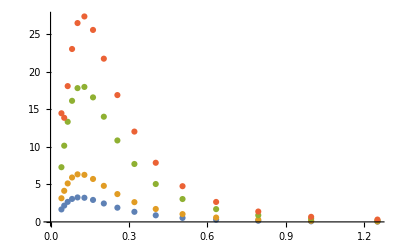

```mathematica
ListPlot[Abs[velListnum]]
```

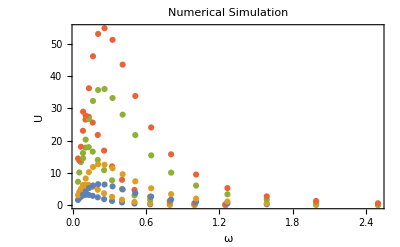

```mathematica
Show[{ListPlot[Abs[velListnum]], ListPlot[2*Abs[velListnum]]},PlotRange->All,AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Numerical Simulation", Black], FrameLabel->{"ω","U"}]
```

```mathematica
w[f_] = 2*π*f;
θ1[f_] := (m1*f)/(3*η*a1);
θ2[f_] := (m2*f)/(3*η*a2);
θbar[f_] := ((m1+m2)*f)/(3*η*(a1+a2));
ω0 := √((k*(m1+m2))/(m1*m2));
UF[f_] = (3*ω0^4)/(2*k^2*θbar[f]^2)*(a1^2*a2^2)/((a1+a2)^3*L^2)*(w[f]*(θ2[f]-θ1[f]))/((ω0^2-w[f]^2+w[f]^2/(θ1[f]*θ2[f]))^2+(ω0^2/θbar[f]-w[f]^2/θ1[f]-w[f]^2/θ2[f])^2);
 
flist = Subdivide[0.00001, 1.25*10^-3, 100];
(*multiply by Fa squared*)
(*Show[Table[Plot[Fa^2*UF[f],{f,0,0.01τ}, PlotStyle->ColorData[1][Fa]],{Fa}], PlotRange->All]*)
```

```mathematica
Analyticlist=ConstantArray[Null,{Length[FList],100}];
```

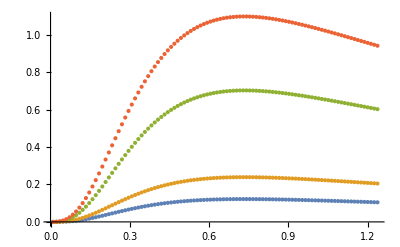

{{{0.01,8.16426×10^-6},{0.0224,0.0000909972},{0.0348,0.000336253},{0.0472,0.000821799},{0.0596,0.00161132},{0.072,0.00275162},{0.0844,0.00427151},{0.0968,0.00618223},{0.1092,0.00847901},{0.1216,0.0111435},{0.134,0.0141468},{0.1464,0.0174521},{0.1588,0.0210176},{0.1712,0.0247992},{0.1836,0.0287523},{0.196,0.0328332},{0.2084,0.0370007},{0.2208,0.0412166},{0.2332,0.0454462},{0.2456,0.0496585},{0.258,0.0538264},{0.2704,0.0579264},{0.2828,0.0619386},{0.2952,0.0658463},{0.3076,0.0696359},{0.32,0.0732964},{0.3324,0.0768194},{0.3448,0.0801984},{0.3572,0.083429},{0.3696,0.0865084},{0.382,0.0894351},{0.3944,0.0922089},{0.4068,0.0948308},{0.4192,0.0973023},{0.4316,0.099626},{0.444,0.101805},{0.4564,0.103843},{0.4688,0.105743},{0.4812,0.10751},{0.4936,0.109148},{0.506,0.110663},{0.5184,0.112058},{0.5308,0.113338},{0.5432,0.114508},{0.5556,0.115574},{0.568,0.116539},{0.5804,0.117408},{0.5928,0.118187},{0.6052,0.118878},{0.6176,0.119487},{0.63,0.120019},{0.6424,0.120476},{0.6548,0.120863},{0.6672,0.121184},{0.6796,0.121443},{0.692,0.121642},{0.7044,0.121786},{0.7168,0.121877},{0.7292,0.121919},{0.7416,0.121915},{0.754,0.121866},{0.7664,0.121777},{0.7788,0.12165},{0.7912,0.121487},{0.8036,0.12129},{0.816,0.121061},{0.8284,0.120804},{0.8408,0.120518},{0.8532,0.120208},{0.8656,0.119873},{0.878,0.119517},{0.8904,0.119139},{0.9028,0.118743},{0.9152,0.118329},{0.9276,0.117899},{0.94,0.117454},{0.9524,0.116995},{0.9648,0.116524},{0.9772,0.116041},{0.9896,0.115547},{1.002,0.115043},{1.0144,0.114531},{1.0268,0.11401},{1.0392,0.113483},{1.0516,0.112949},{1.064,0.112409},{1.0764,0.111864},{1.0888,0.111315},{1.1012,0.110761},{1.1136,0.110205},{1.126,0.109645},{1.1384,0.109083},{1.1508,0.108519},{1.1632,0.107954},{1.1756,0.107387},{1.188,0.10682},{1.2004,0.106253},{1.2128,0.105685},{1.2252,0.105117},{1.2376,0.10455}},{{0.01,0.0000160019},{0.0224,0.000178355},{0.0348,0.000659055},{0.0472,0.00161073},{0.0596,0.00315819},{0.072,0.00539317},{0.0844,0.00837216},{0.0968,0.0121172},{0.1092,0.0166189},{0.1216,0.0218413},{0.134,0.0277278},{0.1464,0.034206},{0.1588,0.0411945},{0.1712,0.0486065},{0.1836,0.0563544},{0.196,0.064353},{0.2084,0.0725214},{0.2208,0.0807845},{0.2332,0.0890745},{0.2456,0.0973306},{0.258,0.1055},{0.2704,0.113536},{0.2828,0.1214},{0.2952,0.129059},{0.3076,0.136486},{0.32,0.143661},{0.3324,0.150566},{0.3448,0.157189},{0.3572,0.163521},{0.3696,0.169556},{0.382,0.175293},{0.3944,0.18073},{0.4068,0.185868},{0.4192,0.190713},{0.4316,0.195267},{0.444,0.199538},{0.4564,0.203531},{0.4688,0.207256},{0.4812,0.210719},{0.4936,0.213931},{0.506,0.216899},{0.5184,0.219633},{0.5308,0.222142},{0.5432,0.224436},{0.5556,0.226525},{0.568,0.228416},{0.5804,0.23012},{0.5928,0.231646},{0.6052,0.233001},{0.6176,0.234195},{0.63,0.235237},{0.6424,0.236133},{0.6548,0.236892},{0.6672,0.237521},{0.6796,0.238028},{0.692,0.238419},{0.7044,0.2387},{0.7168,0.238879},{0.7292,0.238961},{0.7416,0.238953},{0.754,0.238858},{0.7664,0.238684},{0.7788,0.238434},{0.7912,0.238114},{0.8036,0.237728},{0.816,0.23728},{0.8284,0.236775},{0.8408,0.236216},{0.8532,0.235607},{0.8656,0.234951},{0.878,0.234252},{0.8904,0.233513},{0.9028,0.232737},{0.9152,0.231926},{0.9276,0.231083},{0.94,0.23021},{0.9524,0.229311},{0.9648,0.228387},{0.9772,0.22744},{0.9896,0.226472},{1.002,0.225484},{1.0144,0.22448},{1.0268,0.22346},{1.0392,0.222426},{1.0516,0.221379},{1.064,0.220321},{1.0764,0.219253},{1.0888,0.218177},{1.1012,0.217092},{1.1136,0.216001},{1.126,0.214904},{1.1384,0.213803},{1.1508,0.212698},{1.1632,0.21159},{1.1756,0.210479},{1.188,0.209368},{1.2004,0.208255},{1.2128,0.207142},{1.2252,0.20603},{1.2376,0.204918}},{{0.01,0.0000470261},{0.0224,0.000524144},{0.0348,0.00193682},{0.0472,0.00473356},{0.0596,0.00928121},{0.072,0.0158493},{0.0844,0.0246039},{0.0968,0.0356096},{0.1092,0.0488391},{0.1216,0.0641868},{0.134,0.0814856},{0.1464,0.100524},{0.1588,0.121061},{0.1712,0.142843},{0.1836,0.165613},{0.196,0.189119},{0.2084,0.213124},{0.2208,0.237408},{0.2332,0.26177},{0.2456,0.286033},{0.258,0.31004},{0.2704,0.333656},{0.2828,0.356766},{0.2952,0.379275},{0.3076,0.401103},{0.32,0.422188},{0.3324,0.44248},{0.3448,0.461943},{0.3572,0.480551},{0.3696,0.498288},{0.382,0.515146},{0.3944,0.531123},{0.4068,0.546225},{0.4192,0.560461},{0.4316,0.573846},{0.444,0.586396},{0.4564,0.598133},{0.4688,0.609079},{0.4812,0.619257},{0.4936,0.628694},{0.506,0.637417},{0.5184,0.645452},{0.5308,0.652826},{0.5432,0.659568},{0.5556,0.665705},{0.568,0.671264},{0.5804,0.676271},{0.5928,0.680754},{0.6052,0.684738},{0.6176,0.688248},{0.63,0.691308},{0.6424,0.693942},{0.6548,0.696172},{0.6672,0.698021},{0.6796,0.69951},{0.692,0.700659},{0.7044,0.701487},{0.7168,0.702012},{0.7292,0.702254},{0.7416,0.702228},{0.754,0.701951},{0.7664,0.701438},{0.7788,0.700705},{0.7912,0.699764},{0.8036,0.698629},{0.816,0.697314},{0.8284,0.695829},{0.8408,0.694186},{0.8532,0.692396},{0.8656,0.690469},{0.878,0.688415},{0.8904,0.686243},{0.9028,0.683961},{0.9152,0.681578},{0.9276,0.6791},{0.94,0.676537},{0.9524,0.673894},{0.9648,0.671177},{0.9772,0.668394},{0.9896,0.665549},{1.002,0.662648},{1.0144,0.659697},{1.0268,0.656699},{1.0392,0.653661},{1.0516,0.650585},{1.064,0.647475},{1.0764,0.644337},{1.0888,0.641172},{1.1012,0.637985},{1.1136,0.634779},{1.126,0.631556},{1.1384,0.628319},{1.1508,0.625071},{1.1632,0.621815},{1.1756,0.618552},{1.188,0.615284},{1.2004,0.612014},{1.2128,0.608744},{1.2252,0.605475},{1.2376,0.602209}},{{0.01,0.0000734783},{0.0224,0.000818975},{0.0348,0.00302627},{0.0472,0.00739619},{0.0596,0.0145019},{0.072,0.0247646},{0.0844,0.0384436},{0.0968,0.0556401},{0.1092,0.0763111},{0.1216,0.100292},{0.134,0.127321},{0.1464,0.157069},{0.1588,0.189158},{0.1712,0.223193},{0.1836,0.25877},{0.196,0.295499},{0.2084,0.333006},{0.2208,0.370949},{0.2332,0.409016},{0.2456,0.446926},{0.258,0.484437},{0.2704,0.521337},{0.2828,0.557447},{0.2952,0.592617},{0.3076,0.626723},{0.32,0.659668},{0.3324,0.691375},{0.3448,0.721786},{0.3572,0.750861},{0.3696,0.778576},{0.382,0.804916},{0.3944,0.82988},{0.4068,0.853477},{0.4192,0.875721},{0.4316,0.896634},{0.444,0.916244},{0.4564,0.934583},{0.4688,0.951685},{0.4812,0.967589},{0.4936,0.982335},{0.506,0.995964},{0.5184,1.00852},{0.5308,1.02004},{0.5432,1.03058},{0.5556,1.04016},{0.568,1.04885},{0.5804,1.05667},{0.5928,1.06368},{0.6052,1.0699},{0.6176,1.07539},{0.63,1.08017},{0.6424,1.08428},{0.6548,1.08777},{0.6672,1.09066},{0.6796,1.09298},{0.692,1.09478},{0.7044,1.09607},{0.7168,1.09689},{0.7292,1.09727},{0.7416,1.09723},{0.754,1.0968},{0.7664,1.096},{0.7788,1.09485},{0.7912,1.09338},{0.8036,1.09161},{0.816,1.08955},{0.8284,1.08723},{0.8408,1.08467},{0.8532,1.08187},{0.8656,1.07886},{0.878,1.07565},{0.8904,1.07225},{0.9028,1.06869},{0.9152,1.06496},{0.9276,1.06109},{0.94,1.05709},{0.9524,1.05296},{0.9648,1.04871},{0.9772,1.04437},{0.9896,1.03992},{1.002,1.03539},{1.0144,1.03078},{1.0268,1.02609},{1.0392,1.02134},{1.0516,1.01654},{1.064,1.01168},{1.0764,1.00678},{1.0888,1.00183},{1.1012,0.996852},{1.1136,0.991842},{1.126,0.986806},{1.1384,0.981749},{1.1508,0.976674},{1.1632,0.971585},{1.1756,0.966487},{1.188,0.961382},{1.2004,0.956273},{1.2128,0.951163},{1.2252,0.946055},{1.2376,0.940951}}}

```mathematica
Do[Fa=FList[[i]];f= flist[[j]];sol1= NSolve[UF[f_] =10^6*Fa^2* (3*ω0^4)/(2*k^2*θbar[f]^2)*(a1^2*a2^2)/((a1+a2)^3*L^2)*(w[f]*(θ2[f]-θ1[f]))/((ω0^2-w[f]^2+w[f]^2/(θ1[f]*θ2[f]))^2+(ω0^2/θbar[f]-w[f]^2/θ1[f]-w[f]^2/θ2[f])^2), f];
Analyticlist[[i,j]]={f*10^3, Evaluate[UF[f]/. sol1]};,{i,1,Length[FList]},{j,1, 100}]
ListPlot[Abs[Analyticlist]]

Analyticlist
```

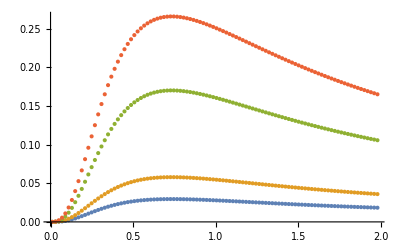

```mathematica
ListPlot[Abs[Analyticlist]]
```

```mathematica
Table[NSolve[Fa^2*UF[f], f],{f,0.0001,2,50}]
```

{{}}

{}

```mathematica
NSol
```

NSolve

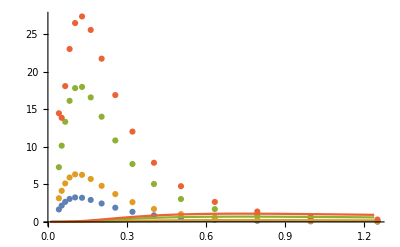

```mathematica
Show[{ListPlot[Abs[velListnum]]},ListPlot[Analyticlist, Joined->True],PlotRange->All]
```

{0.05,0.07,0.12,0.15}

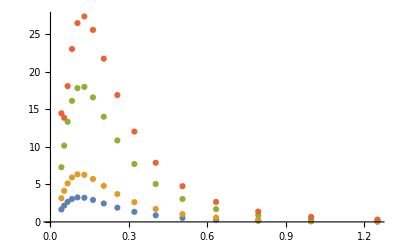

```mathematica
Fa1 = FList

Show[Table[Plot[10^7*Fa1^2*UF[10^3*f1],{f1,0,0.002}],{Fa1}],ListPlot[Abs[velListnum]],  PlotRange-> All]
```

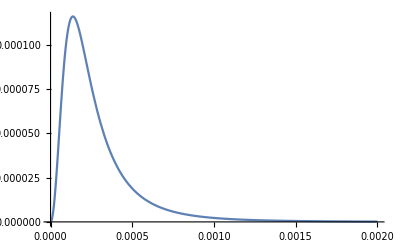

```mathematica
Plot[UF[f], {f,0, 0.002}]
```

```mathematica
Export["numericaltest.csv", velListnum]
```

numericaltest.csv

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/christian.neureuter/Christian's Documents/Physics/Computational Physics

```mathematica
Export["numericaltest.csv", Flatten[velListnum]]
```

numericaltest.csv

```mathematica
(* vary rad and rho *)
xiAllO2TranslationFuncVarRadRho[b_,Ec1x_,gamma_,nu_,rhoF_,rho1_,rho2_]:=-((24 b^2 Ec1x^2 gamma^2 nu^2 (-2+3 nu) (-2+3 b nu) ((4-6 nu) rho1+(2-3 nu) rhoF+3 b^3 nu (2 rho2+rhoF+2 nu^2 rhoF)-2 b^2 (2 rho2+rhoF+3 nu^3 rhoF)))/((-1+b (-1+3 nu)) (1296 b^12 gamma^6 nu^12 rhoF^4-5832 b^13 gamma^6 nu^14 rhoF^4+6561 b^14 gamma^6 nu^16 rhoF^4+64 (4+gamma^2 (2 rho1+rhoF)^2)-32 b (-16+48 nu+9 gamma^2 nu^2 (2 rho1+rhoF)^2)-288 b^9 gamma^4 nu^6 rhoF^2 (2 rho2 (-2+gamma^2 (2 rho1+rhoF))+rhoF (-2-12 nu^3+gamma^2 (2 rho1+rhoF)))+1296 b^10 gamma^4 nu^8 rhoF^2 (2 rho2 (-2+gamma^2 (2 rho1+rhoF))+rhoF (-2-12 nu^3+gamma^2 (2 rho1+rhoF)))-1458 b^11 gamma^4 nu^10 rhoF^2 (2 rho2 (-2+gamma^2 (2 rho1+rhoF))+rhoF (-2-12 nu^3+gamma^2 (2 rho1+rhoF)))-64 b^3 gamma^2 (rhoF (4+4 gamma^2 rho1^2-2 (1+6 nu^3) rhoF+gamma^2 rhoF^2-4 rho1 (1+6 nu^3-gamma^2 rhoF))+2 rho2 (4+4 gamma^2 rho1^2-2 rhoF+gamma^2 rhoF^2+4 rho1 (-1+gamma^2 rhoF)))+4 b^2 (64 (1-3 nu)^2+16 gamma^4 (2 rho1+rhoF)^2+gamma^2 (64+324 nu^4 rho1^2-16 (2-3 nu)^2 rhoF+81 nu^4 rhoF^2+4 rho1 (-32+96 nu-72 nu^2+81 nu^4 rhoF)))+16 b^6 gamma^2 (4 rho2^2 (4-4 gamma^2 (-1+2 rho1+rhoF)+gamma^4 (2 rho1+rhoF)^2)+4 rho2 rhoF (4+24 nu^3+gamma^4 (2 rho1+rhoF)^2-4 gamma^2 (-1+(2+6 nu^3) rho1+rhoF+3 nu^3 rhoF))+rhoF^2 (4 (1+6 nu^3)^2+gamma^4 (2 rho1+rhoF)^2+4 gamma^2 (1+2 (-1-6 nu^3+9 nu^6) rho1+(-1-6 nu^3+9 nu^6) rhoF)))+96 b^4 gamma^2 nu (2 rho2 (8+3 nu (2 rho1+rhoF) (-2+gamma^2 (2 rho1+rhoF)))+rhoF (8+16 nu^2-24 nu^3-36 nu^4 (2 rho1+rhoF)+3 nu (2 rho1+rhoF) (-2+gamma^2 (2 rho1+rhoF))))-36 b^5 gamma^2 nu^2 (2 rho2 (-2+gamma^2 (2 rho1+rhoF)) (-8+9 nu^2 (2 rho1+rhoF))+rhoF (16-96 nu^3-8 gamma^2 (2 rho1+rhoF)-108 nu^5 (2 rho1+rhoF)+nu^2 (-32+18 rho1+9 rhoF) (-2+gamma^2 (2 rho1+rhoF))))+81 b^8 gamma^2 nu^4 (4 rho2^2 (-2+gamma^2 (2 rho1+rhoF))^2+4 rho2 rhoF (-2+gamma^2 (2 rho1+rhoF)) (-2-12 nu^3+gamma^2 (2 rho1+rhoF))+rhoF^2 (32 gamma^2 nu^4-24 nu^3 (-2+gamma^2 (2 rho1+rhoF))+(-2+gamma^2 (2 rho1+rhoF))^2+36 nu^6 (4+gamma^2 (2 rho1+rhoF))))-72 b^7 gamma^2 nu^2 (4 rho2^2 (-2+gamma^2 (2 rho1+rhoF))^2+4 rho2 rhoF (4+24 nu^3+gamma^4 (2 rho1+rhoF)^2-4 gamma^2 (2 nu^2+2 rho1+rhoF+3 nu^3 (2 rho1+rhoF)))+rhoF^2 (4 (1+6 nu^3)^2+gamma^4 (2 rho1+rhoF)^2+4 gamma^2 (-4 nu^2-4 nu^4-2 rho1-rhoF-6 nu^3 (2 rho1+rhoF)+9 nu^6 (2 rho1+rhoF)))))))
(*
xiAllO2TranslationFuncVarRadRho[A1/(k*a),b/a, 6Pi*eta*a*gamma[[2]]/k,a/l,10rho1/rhoF,rho1/rhoF, rhoResc*rhoF]*a/tv*)
```

{{{0.0416667,1.70048},{0.0522713,2.21531},{0.065575,2.71206},{0.0822646,3.09791},{0.103202,3.2875},{0.129468,3.23218},{0.162419,2.93677},{0.203757,2.45976},{0.255615,1.89587},{0.320672,1.34441},{0.402287,0.878215},{0.504674,0.529601},{0.63312,0.295764},{0.794256,0.153757},{0.996404,0.0750092},{1.25,0.0347032}},{{0.0416667,3.33294},{0.0522713,4.34201},{0.065575,5.31564},{0.0822646,6.07191},{0.103202,6.4435},{0.129468,6.33507},{0.162419,5.75607},{0.203757,4.82114},{0.255615,3.7159},{0.320672,2.63504},{0.402287,1.7213},{0.504674,1.03802},{0.63312,0.579697},{0.794256,0.301364},{0.996404,0.147018},{1.25,0.0680182}},{{0.0416667,9.79475},{0.0522713,12.7602},{0.065575,15.6215},{0.0822646,17.844},{0.103202,18.936},{0.129468,18.6173},{0.162419,16.9158},{0.203757,14.1682},{0.255615,10.9202},{0.320672,7.74378},{0.402287,5.05852},{0.504674,3.0505},{0.63312,1.7036},{0.794256,0.885642},{0.996404,0.432053},{1.25,0.19989}},{{0.0416667,15.3043},{0.0522713,19.9378},{0.065575,24.4085},{0.0822646,27.8812},{0.103202,29.5875},{0.129468,29.0896},{0.162419,26.4309},{0.203757,22.1379},{0.255615,17.0628},{0.320672,12.0997},{0.402287,7.90394},{0.504674,4.76641},{0.63312,2.66187},{0.794256,1.38382},{0.996404,0.675083},{1.25,0.312328}}}

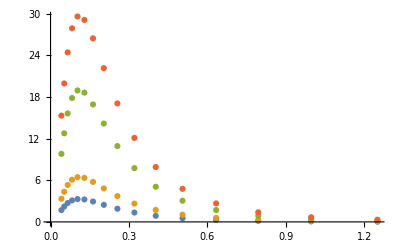

```mathematica
rhoResc=(tv^2k)^(-1)*(4/3Pi*a1^3);

tv=(6 Pi*η*a1/k);
dataana=Table[{10^3*1/T,10^6a1/(6Pi*η*a1/k)*xiAllO2TranslationFuncVarRadRho[a2/a1,A1/(k*a1),6Pi*η*a1*2Pi/T/k,a1/L,rhoResc*0,rhoResc*ρs,(*(b/a)^3*)rhoResc*ρs]},{A1,FList},{T,TListNum}]//Abs
dataana//ListPlot
```

```mathematica
Show[{ListPlot[Abs[velListnum]]},ListPlot[dataana, Joined->True],PlotRange->All,AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Test Title", Black], FrameLabel->{"x","y"}]
```

ListPlot::lpn: Abs[velListnum] is not a list of numbers or pairs of numbers.

ListPlot::lpn: dataana is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Abs[velListnum]]},ListPlot[dataana,Joined→True],PlotRange→All,AxesStyle→GrayLevel[0],Frame→True,FrameStyle→GrayLevel[0],PlotLabel→Test Title,FrameLabel→{x,y}].

Show[{ListPlot[Abs[velListnum]]},ListPlot[dataana,Joined→True],PlotRange→All,AxesStyle→GrayLevel[0],Frame→True,FrameStyle→GrayLevel[0],PlotLabel→Test Title,FrameLabel→{x,y}]

```mathematica
Show[{ListPlot[Abs[velListnum]], ListPlot[2*Abs[velListnum]]},PlotRange->All,AxesStyle->Black,Frame->True,FrameStyle->Black,PlotLabel->Style["Numerical Simulation", Black], FrameLabel->{"ω","U"}]
```

-Graphics-

# Export these data lists, plot in python, export figures. Finish collecting figures, collect literature and make rough outline.